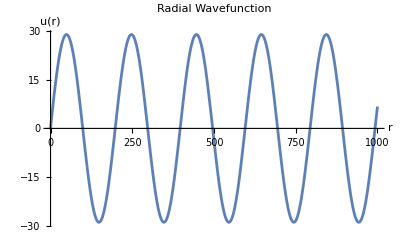

```mathematica
(*Constants*)
M=1;
m=0.1*M;
α=0.01;
E0=m^2/10; (*Try different negative E for bound states*)
k=Sqrt[E0*M];

(*Potential*)
V[r_]:=-α*Exp[-m*r]/r;

(*Schrödinger equation*)
eq=u''[r]==(M*V[r]-k^2) u[r];

(*Boundary conditions*)
r0=10^-6;
bc={u[r0]==r0,u'[r0]==1}; (*δ is a small value instead of r=0*)

(*Numerical solution*)
maxr = 1000;
sol=NDSolve[{eq,Sequence@@bc},u,{r,r0,maxr},MaxSteps->Infinity];

(*Plot the solution*)
Plot[Evaluate[u[r]/. sol],{r,r0,maxr},PlotRange->All,AxesLabel->{"r","u(r)"},PlotLabel->"Radial Wavefunction"]
```

```mathematica
Clear[δ]
fitRegion={r,0.8*maxr,maxr};
numericalData=Table[{r,u[r]/. sol[[1]]},{r,0.8*maxr,maxr,maxr/100}];

fitModel=NonlinearModelFit[numericalData,A*Sin[k*r+δ],{{A,1},{δ,0}},r];
fitModel["BestFitParameters"]
```

{A→28.8906,δ→0.0277532}